```mathematica
ClearAll["Global`*"]
```

```mathematica
d2[n_,k_]:=Sum[ d2[n/j,k-1],{j,2,n}];d2[n_,0]:=1
d2b[n_,k_,a_]:= d2b[n,k,a]=Sum[a d2b[n/ (j a),k-1,a],{j,2,n/a^k}];d2b[n_,0,a_]:=1
d1[n_,k_]:=Sum[ d1[n/j,k-1],{j,1,n}];d1[n_,0]:=1
d1a[n_,k_,a_]:=Sum[a d1a[n/ j,k-1,a],{j,a,n/(a^(k-1)),a}];d1a[n_,0,a_]:=1
d1b[n_,k_,a_]:=Sum[a d1b[n/ (j a),k-1,a],{j,1,n/(a^k)}];d1b[n_,0,a_]:=1
d2c[n_,k_,a_]:= a^k d2[ n a^-k, k]
d22[n_,k_,a_]:= a^-k d2b[ n a^k, k,a]
d1c[n_,k_,a_]:= a^k d1[ n a^-k, k]
d11[n_,k_,a_]:= a^-k d1b[ n a^k, k,a]

d2bb[n_,k_,a_]:= d2bb[n,k,a]=Sum[a d2bb[n/ (j a),k-1,a],{j,1+1/a,n/(a^k)}];d2bb[n_,0,a_]:=1
d2bb2[n_,k_,a_]:= d2bb2[n,k,a]=Sum[a d2bb2[n/ ((j+1/a) a),k-1,a],{j,1,Floor[n/(a^k) - 1/a]}];d2bb2[n_,0,a_]:=1
d2ap[n_,j_]:=(-1)^j (1-(Gamma[j,-Log[n]])/Gamma[j])
dh[n_,k_,a_]:=Sum[Binomial[k,j] dh[n/(m^(k-j)),j,m+1],{m,a,n^(1/k)},{j,0,k-1}]
dh[n_,1,a_]:=Floor[n]-a+1;dh[n_,0,a_]:=1

fe[n_, k_, a_]:=(1/(a^k))(dh[n*(a^k),k,a+1])
d2bbalt2[n_, k_, a_]:=(a^k)(dh[n*(a^-k),k,(1/a)+1])
lin[n_, a_]:=Sum[ (-1)^(k+1)/k fe[n,k,a],{k,1, 100}]
```

```mathematica
Table[{n,aa=d1b[n,k=3,a=1/3],bb=( a^k) d1[n/( a^k),k],aa-bb},{n,1,60}]//TableForm
```

1 | 76/9 | 76/9 | 0
2 | 208/9 | 208/9 | 0
3 | 1099/27 | 1099/27 | 0
4 | 1633/27 | 1633/27 | 0
5 | 2186/27 | 2186/27 | 0
6 | 2810/27 | 2810/27 | 0
7 | 3413/27 | 3413/27 | 0
8 | 458/3 | 458/3 | 0
9 | 1598/9 | 1598/9 | 0
10 | 1835/9 | 1835/9 | 0
11 | 2069/9 | 2069/9 | 0
12 | 2332/9 | 2332/9 | 0
13 | 7711/27 | 7711/27 | 0
14 | 8518/27 | 8518/27 | 0
15 | 9295/27 | 9295/27 | 0
16 | 10153/27 | 10153/27 | 0
17 | 10903/27 | 10903/27 | 0
18 | 11791/27 | 11791/27 | 0
19 | 12629/27 | 12629/27 | 0
20 | 13517/27 | 13517/27 | 0
21 | 14303/27 | 14303/27 | 0
22 | 15212/27 | 15212/27 | 0
23 | 16070/27 | 16070/27 | 0
24 | 17042/27 | 17042/27 | 0
25 | 17927/27 | 17927/27 | 0
26 | 18833/27 | 18833/27 | 0
27 | 6592/9 | 6592/9 | 0
28 | 6908/9 | 6908/9 | 0
29 | 7202/9 | 7202/9 | 0
30 | 2509/3 | 2509/3 | 0
31 | 7820/9 | 7820/9 | 0
32 | 8183/9 | 8183/9 | 0
33 | 8477/9 | 8477/9 | 0
34 | 8804/9 | 8804/9 | 0
35 | 3046/3 | 3046/3 | 0
36 | 9482/9 | 9482/9 | 0
37 | 9775/9 | 9775/9 | 0
38 | 30451/27 | 30451/27 | 0
39 | 31381/27 | 31381/27 | 0
40 | 32536/27 | 32536/27 | 0
41 | 33460/27 | 33460/27 | 0
42 | 34489/27 | 34489/27 | 0
43 | 35533/27 | 35533/27 | 0
44 | 36571/27 | 36571/27 | 0
45 | 37531/27 | 37531/27 | 0
46 | 38629/27 | 38629/27 | 0
47 | 39667/27 | 39667/27 | 0
48 | 40825/27 | 40825/27 | 0
49 | 41842/27 | 41842/27 | 0
50 | 42947/27 | 42947/27 | 0
51 | 43940/27 | 43940/27 | 0
52 | 45101/27 | 45101/27 | 0
53 | 46106/27 | 46106/27 | 0
54 | 47273/27 | 47273/27 | 0
55 | 48323/27 | 48323/27 | 0
56 | 49493/27 | 49493/27 | 0
57 | 50468/27 | 50468/27 | 0
58 | 51626/27 | 51626/27 | 0
59 | 52664/27 | 52664/27 | 0
60 | 53912/27 | 53912/27 | 0

```mathematica
N[Table[{n,aa=d1b[n,k=2,a=1/10],bb=( a^k) d1[n/( a^k),k],aa-bb},{n,50,60}]//TableForm]
```

50. | 433.76 | 433.76 | 0.
51. | 443.41 | 443.41 | 0.
52. | 453.08 | 453.08 | 0.
53. | 462.7 | 462.7 | 0.
54. | 472.65 | 472.65 | 0.
55. | 482.28 | 482.28 | 0.
56. | 492.12 | 492.12 | 0.
57. | 501.99 | 501.99 | 0.
58. | 511.74 | 511.74 | 0.
59. | 521.46 | 521.46 | 0.
60. | 531.41 | 531.41 | 0.

```mathematica
N[Table[{n,aa=d1a[n( a^k),k=2,a=1/4]/(a^k),bb= d1[n,k],aa-bb},{n,1,50}]//TableForm]
```

1. | 8. | 1. | 7.
2. | 3. | 3. | 0.
3. | 5. | 5. | 0.
4. | 8. | 8. | 0.
5. | 10. | 10. | 0.
6. | 14. | 14. | 0.
7. | 16. | 16. | 0.
8. | 20. | 20. | 0.
9. | 23. | 23. | 0.
10. | 27. | 27. | 0.
11. | 29. | 29. | 0.
12. | 35. | 35. | 0.
13. | 37. | 37. | 0.
14. | 41. | 41. | 0.
15. | 45. | 45. | 0.
16. | 50. | 50. | 0.
17. | 52. | 52. | 0.
18. | 58. | 58. | 0.
19. | 60. | 60. | 0.
20. | 66. | 66. | 0.
21. | 70. | 70. | 0.
22. | 74. | 74. | 0.
23. | 76. | 76. | 0.
24. | 84. | 84. | 0.
25. | 87. | 87. | 0.
26. | 91. | 91. | 0.
27. | 95. | 95. | 0.
28. | 101. | 101. | 0.
29. | 103. | 103. | 0.
30. | 111. | 111. | 0.
31. | 113. | 113. | 0.
32. | 119. | 119. | 0.
33. | 123. | 123. | 0.
34. | 127. | 127. | 0.
35. | 131. | 131. | 0.
36. | 140. | 140. | 0.
37. | 142. | 142. | 0.
38. | 146. | 146. | 0.
39. | 150. | 150. | 0.
40. | 158. | 158. | 0.
41. | 160. | 160. | 0.
42. | 168. | 168. | 0.
43. | 170. | 170. | 0.
44. | 176. | 176. | 0.
45. | 182. | 182. | 0.
46. | 186. | 186. | 0.
47. | 188. | 188. | 0.
48. | 198. | 198. | 0.
49. | 201. | 201. | 0.
50. | 207. | 207. | 0.

```mathematica
Table[{n,aa=(d1a[n,k=2,a=.27]-d1a[n-1,k,a]),bb=(( a^k) d1[n/( a^k),k]-( a^k) d1[(n-1)/( a^k),k]),aa-bb},{n,1,40}]//TableForm
```

1 | 2.6973 | 2.6973 | 1.33227×10^-15
2 | 4.2282 | 4.2282 | -4.44089×10^-15
3 | 4.7385 | 4.7385 | 1.06581×10^-14
4 | 4.8843 | 4.8843 | 3.55271×10^-15
5 | 5.3217 | 5.3217 | 7.10543×10^-15
6 | 5.6133 | 5.6133 | -3.55271×10^-15
7 | 5.9778 | 5.9778 | -7.10543×10^-14
8 | 5.1759 | 5.1759 | -1.20792×10^-13
9 | 6.0507 | 6.0507 | 0.
10 | 6.1236 | 6.1236 | -1.42109×10^-14
11 | 6.0507 | 6.0507 | -1.42109×10^-14
12 | 6.1236 | 6.1236 | 0.
13 | 6.3423 | 6.3423 | 5.18696×10^-13
14 | 6.9984 | 6.9984 | -8.52651×10^-14
15 | 5.7591 | 5.7591 | 1.42109×10^-14
16 | 6.4152 | 6.4152 | 8.52651×10^-14
17 | 6.7797 | 6.7797 | 4.26326×10^-14
18 | 6.561 | 6.561 | -1.42109×10^-14
19 | 6.9255 | 6.9255 | 1.42109×10^-14
20 | 6.7068 | 6.7068 | 1.42109×10^-14
21 | 7.4358 | 7.4358 | -4.26326×10^-14
22 | 6.1965 | 6.1965 | 2.84217×10^-14
23 | 6.9984 | 6.9984 | 0.
24 | 6.6339 | 6.6339 | 2.84217×10^-13
25 | 7.1442 | 7.1442 | 6.25278×10^-13
26 | 6.7068 | 6.7068 | 3.41061×10^-13
27 | 7.3629 | 7.3629 | -1.98952×10^-13
28 | 7.4358 | 7.4358 | -1.13687×10^-13
29 | 6.561 | 6.561 | 0.
30 | 7.2171 | 7.2171 | 1.7053×10^-13
31 | 7.4358 | 7.4358 | 2.84217×10^-14
32 | 6.7068 | 6.7068 | 5.68434×10^-14
33 | 7.6545 | 7.6545 | 2.84217×10^-14
34 | 7.29 | 7.29 | 1.13687×10^-13
35 | 8.019 | 8.019 | 2.84217×10^-14
36 | 6.1965 | 6.1965 | 8.52651×10^-14
37 | 7.8732 | 7.8732 | 5.68434×10^-14
38 | 7.29 | 7.29 | 1.13687×10^-13
39 | 7.3629 | 7.3629 | 8.52651×10^-14
40 | 7.29 | 7.29 | 8.52651×10^-14

```mathematica
Table[{ n, Floor[ 5/n*3]/9, d1as[5,1/3,n]},{n,1/3,15,1/3}]//TableForm
```

1/3 | 5 | 5
2/3 | 22/9 | 22/9
1 | 5/3 | 5/3
4/3 | 11/9 | 11/9
5/3 | 1 | 1
2 | 7/9 | 7/9
7/3 | 2/3 | 2/3
8/3 | 5/9 | 5/9
3 | 5/9 | 5/9
10/3 | 4/9 | 4/9
11/3 | 4/9 | 4/9
4 | 1/3 | 1/3
13/3 | 1/3 | 1/3
14/3 | 1/3 | 1/3
5 | 1/3 | 1/3
16/3 | 2/9 | 2/9
17/3 | 2/9 | 2/9
6 | 2/9 | 2/9
19/3 | 2/9 | 2/9
20/3 | 2/9 | 2/9
7 | 2/9 | 2/9
22/3 | 2/9 | 2/9
23/3 | 1/9 | 1/9
8 | 1/9 | 1/9
25/3 | 1/9 | 1/9
26/3 | 1/9 | 1/9
9 | 1/9 | 1/9
28/3 | 1/9 | 1/9
29/3 | 1/9 | 1/9
10 | 1/9 | 1/9
31/3 | 1/9 | 1/9
32/3 | 1/9 | 1/9
11 | 1/9 | 1/9
34/3 | 1/9 | 1/9
35/3 | 1/9 | 1/9
12 | 1/9 | 1/9
37/3 | 1/9 | 1/9
38/3 | 1/9 | 1/9
13 | 1/9 | 1/9
40/3 | 1/9 | 1/9
41/3 | 1/9 | 1/9
14 | 1/9 | 1/9
43/3 | 1/9 | 1/9
44/3 | 1/9 | 1/9
15 | 1/9 | 1/9

```mathematica
Table[{n,aa=d2b[n,k=3,a=.6],bb=( a^k) d2[n/( a^k),k],aa-bb},{n,1,60}]//TableForm
```

1 | 0. | 0. | 0.
2 | 0.216 | 0.216 | 0.
3 | 0.864 | 0.864 | 0.
4 | 2.16 | 2.16 | 0.
5 | 2.808 | 2.808 | 4.44089×10^-16
6 | 4.968 | 4.968 | 0.
7 | 8.208 | 8.208 | 0.
8 | 10.8 | 10.8 | -5.32907×10^-15
9 | 12.744 | 12.744 | -5.32907×10^-15
10 | 15.336 | 15.336 | -5.32907×10^-15
11 | 19.872 | 19.872 | 0.
12 | 22.464 | 22.464 | 0.
13 | 28.944 | 28.944 | 0.
14 | 31.752 | 31.752 | -3.55271×10^-15
15 | 33.696 | 33.696 | 0.
16 | 40.824 | 40.824 | 7.10543×10^-15
17 | 43.416 | 43.416 | 7.10543×10^-15
18 | 47.952 | 47.952 | 7.10543×10^-15
19 | 52.488 | 52.488 | 7.10543×10^-15
20 | 59.616 | 59.616 | 7.10543×10^-15
21 | 66.096 | 66.096 | -7.10543×10^-14
22 | 69.984 | 69.984 | -8.52651×10^-14
23 | 74.52 | 74.52 | -9.9476×10^-14
24 | 81.648 | 81.648 | -1.13687×10^-13
25 | 86.832 | 86.832 | -1.13687×10^-13
26 | 97.848 | 97.848 | -1.27898×10^-13
27 | 98.712 | 98.712 | -1.42109×10^-13
28 | 106.488 | 106.488 | -1.27898×10^-13
29 | 112.32 | 112.32 | -1.13687×10^-13
30 | 117.504 | 117.504 | -1.27898×10^-13
31 | 122.04 | 122.04 | -1.42109×10^-13
32 | 133.704 | 133.704 | 5.68434×10^-14
33 | 140.184 | 140.184 | 5.68434×10^-14
34 | 146.664 | 146.664 | 8.52651×10^-14
35 | 157.032 | 157.032 | 8.52651×10^-14
36 | 158.976 | 158.976 | 8.52651×10^-14
37 | 170.64 | 170.64 | 8.52651×10^-14
38 | 173.232 | 173.232 | 5.68434×10^-14
39 | 189.432 | 189.432 | 1.13687×10^-13
40 | 192.672 | 192.672 | 8.52651×10^-14
41 | 196.56 | 196.56 | 8.52651×10^-14
42 | 207.576 | 207.576 | 1.42109×10^-13
43 | 216. | 216. | 5.68434×10^-14
44 | 221.832 | 221.832 | 1.13687×10^-13
45 | 230.904 | 230.904 | 8.52651×10^-14
46 | 239.328 | 239.328 | 1.13687×10^-13
47 | 251.208 | 251.208 | 8.52651×10^-14
48 | 257.04 | 257.04 | 5.68434×10^-14
49 | 266.112 | 266.112 | 3.41061×10^-13
50 | 273.24 | 273.24 | 2.84217×10^-13
51 | 280.368 | 280.368 | 2.84217×10^-13
52 | 298.512 | 298.512 | 2.27374×10^-13
53 | 301.752 | 301.752 | 2.84217×10^-13
54 | 306.936 | 306.936 | 3.97904×10^-13
55 | 319.248 | 319.248 | 4.54747×10^-13
56 | 326.376 | 326.376 | 5.11591×10^-13
57 | 331.56 | 331.56 | 5.11591×10^-13
58 | 343.224 | 343.224 | 5.11591×10^-13
59 | 358.128 | 358.128 | 6.25278×10^-13
60 | 363.312 | 363.312 | 5.11591×10^-13

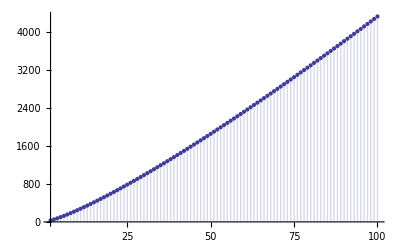

```mathematica
DiscretePlot[d2b[n,3,1/10],{n,2,100}]
```

```mathematica
d2c[100,3,2]
```

32

```mathematica
d2b[100,3,2]
```

32

```mathematica
d22[100,2,3]
```

283

```mathematica
1/(3^3)
```

1/27

```mathematica
3^-3
```

1/27

```mathematica
d11[100,3,.3]
```

1471.

```mathematica
d1[100,3]
```

1471

```mathematica
3^(-3)
```

1/27

```mathematica
3^-3
```

1/27

```mathematica
d2b[n,2,a]
```

```mathematica
ss[n_,a_]:=a^2-2 n+n HarmonicNumber[n/a^2]
```

```mathematica
N[ss[100,3]]
```

111.949

```mathematica
ss[n_,a_]:=a^2 Sum[ 1, {j,2,Floor[n a^-2]},{k,2,Floor[n/(j a^2)]}]
```

```mathematica
ss[1100,4]
```

2640

```mathematica
d2b[1100,2,4]
```

2640

```mathematica
Limit[ss[n,a],{a->0}]
```

{Limit[a^2 ∑_(j=2)^Floor[n/a^2] ∑_(k=2)^Floor[n/(a^2 j)] 1,a→0]}

```mathematica
s2[n_,a_]:=a Sum[ 1, {j,2,Floor[n a^-1]}]
Limit[s2[n,a],{a->0}]
```

{Limit[a (-1+Floor[n/a]),a→0]}

```mathematica
N[s2[100,1/32]]
```

99.9688

```mathematica
N[ss[100,1/128]]
```

1246.37

```mathematica
N[d2bb[100,2,1/80]]
```

360.287

```mathematica
d2bb2[100,2,1/2]
```

318

```mathematica
N[d2bb[100,2,1/3]]
```

331.667

```mathematica
N[d2ap[100,2]]
```

361.517-4.41506×10^-14 ⅈ

```mathematica
N[d2ap[100,3]]
```

698.863-1.71417×10^-13 ⅈ

```mathematica
N[d2bb[100,3,1]]
```

324.

```mathematica
N[d2bb[100,3,1/2]]
```

475.25

```mathematica
N[d2bb[100,3,1/4]]
```

575.656

```mathematica
N[d2bb[100,3,1/8]]
```

634.17

```mathematica
N[d2bb[100,3,1/16]]
```

665.794

```mathematica
Table[{n,d2bb2[n,2,1/2],d2bb2[ n,2,1]},{n,2,50}]//TableForm
```

2 | 0 | 0
3 | 3/4 | 0
4 | 3/2 | 1
5 | 5/2 | 1
6 | 4 | 3
7 | 21/4 | 3
8 | 27/4 | 5
9 | 9 | 6
10 | 21/2 | 8
11 | 12 | 8
12 | 29/2 | 12
13 | 65/4 | 12
14 | 75/4 | 14
15 | 85/4 | 16
16 | 23 | 19
17 | 25 | 19
18 | 57/2 | 23
19 | 30 | 23
20 | 33 | 27
21 | 143/4 | 29
22 | 151/4 | 31
23 | 163/4 | 31
24 | 175/4 | 37
25 | 93/2 | 38
26 | 97/2 | 40
27 | 52 | 42
28 | 55 | 46
29 | 57 | 46
30 | 123/2 | 52
31 | 251/4 | 52
32 | 265/4 | 56
33 | 279/4 | 58
34 | 291/4 | 60
35 | 303/4 | 62
36 | 159/2 | 69
37 | 163/2 | 69
38 | 169/2 | 71
39 | 89 | 73
40 | 183/2 | 79
41 | 94 | 79
42 | 197/2 | 85
43 | 405/4 | 85
44 | 419/4 | 89
45 | 435/4 | 93
46 | 445/4 | 95
47 | 455/4 | 95
48 | 475/4 | 103
49 | 243/2 | 104
50 | 251/2 | 108

```mathematica
Table[{j,a d2bb[n/ (j a),k-1,a]},{j,1+1/a,n/(a^k)}]/.{n->5,k->2,a->3/5}//TableForm
```

Table::iterb: Iterator {j, 1 + 1/a, a^-k\ n} does not have appropriate bounds.

8/3 | 27/25
11/3 | 18/25
14/3 | 9/25
17/3 | 0
20/3 | 0
23/3 | 0
26/3 | 0
29/3 | 0
32/3 | 0
35/3 | 0
38/3 | 0
41/3 | 0

```mathematica
N[d2bb[5,2,1/2]]
```

2.5

```mathematica
(1/4)(d2[20,2]-2d2[10,1]+d2[5,0])
```

5/2

```mathematica
d2[20,2]
```

27

```mathematica
d2[20,1]
```

19

```mathematica
N[d2bb[25,2,1/2]]
```

46.5

```mathematica
N[(1/4)(d2[25*4,2]-2d2[25*2,1]+d2[25,0])]
```

46.5

```mathematica
N[d2bb[25,3,1/2]]
```

40.5

```mathematica
N[(1/8)(d2[25*8,3]-3d2[25*4,2]+3d2[25*2,1]-d2[25,0])]
```

40.5

```mathematica
N[(1/8)(dh[25*8,3,3])]
```

40.5

```mathematica
N[d2bb[10,2,1/3]]
```

11.5556

```mathematica
N[(1/9)(d2[10*9,2]-2d2[10*3,1]+d2[10,0])]
```

21.

```mathematica
N[(1/8)(dh[25*8,3,2]-3dh[25*4,2,2]+3dh[25*2,1,2]-dh[25,0,2])]
```

40.5

```mathematica
N[d2bb[10,3,1/3]]
```

6.77778

```mathematica
N[(1/27)(dh[10*27,3,4])]
```

6.77778

```mathematica
N[d2bb[10,2,1/3]]
```

11.5556

```mathematica
N[(1/9)(dh[10*9,2,4])]
```

11.5556

```mathematica
N[d2bb[100,4,1/3]]
```

556.296

```mathematica
N[(1/81)(dh[100*81,4,4])]
```

556.296

```mathematica
N[d2bb[100,4,1/6]]
```

721.063

```mathematica
N[(1/(6^4))(dh[100*(6^4),4,7])]
```

721.063

```mathematica
N[d2ap[100,2]]
```

361.517-4.41506×10^-14 ⅈ

```mathematica
N[fe[100,2,2265]]
```

361.473

```mathematica
N[d2ap[100,3]]
```

698.863-1.71417×10^-13 ⅈ

```mathematica
fe[100,3,165]
```

695.583

```mathematica
N[d2ap[100,4]]
```

928.88-3.40898×10^-13 ⅈ

```mathematica
fe[100,4,75]
```

910.402

```mathematica
fe[100,2,1]
```

283.

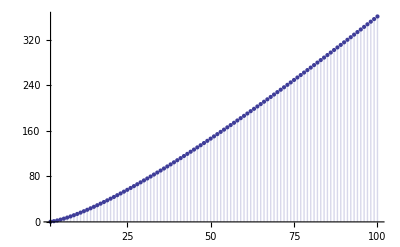

```mathematica
DiscretePlot[fe[n,2,240],{n,2,100}]
```

```mathematica
100 240^2
```

5760000

```mathematica
N[1/240]
```

0.00416667

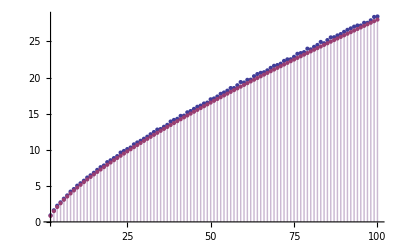

```mathematica
DiscretePlot[{lin[n,4],LogIntegral[n]-Log[Log[n]]-EulerGamma},{n,2,100}]
```

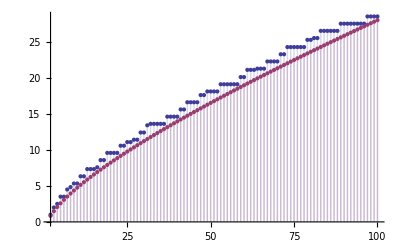

```mathematica
DiscretePlot[{lin[n,1],LogIntegral[n]-Log[Log[n]]-EulerGamma},{n,2,100}]
```

```mathematica
DiscretePlot[{lin[n,10],LogIntegral[n]-Log[Log[n]]-EulerGamma},{n,2,100}]
```

$Aborted

```mathematica
d2bbalt2[100,3,1/2]
```

1901/4

```mathematica
d2bbalt[100,3,1/2]
```

1901/4

```mathematica
d2bb2[100,3,1/2]
```

1901/4

```mathematica
FullSimplify[(1/((1/a)^k))(dhf[n*((1/a)^k),k,(1/a)+1])]
```

(1/a)^-k dhf[(1/a)^k n,k,1+1/a]

```mathematica
(1/a)^-k
```

(1/a)^-k

```mathematica
FullSimplify[(a^-1)^-k]
```

(1/a)^-k

```mathematica
(1/7)^-3
```

343

```mathematica
7^3
```

343

```mathematica
Plot[{0,x/Log[x+1]},{x,0,50}]
```